## Computer practise 1 and 2. Group 2: Nerea Andia, Ander Cano, Mikel Lamela and Aitor Larrinoa

## OPTIONAL

# Practise 1

## 2. The Lotka-Volterra model.

### c) Write a program in Mathematica that shows the evolution of the populations of foxes and rabbits, correspondent to A = 0.5, B = 0.002, C = 0.1, D = 0.001 and initial population of 250 rabbits and 100 foxes.

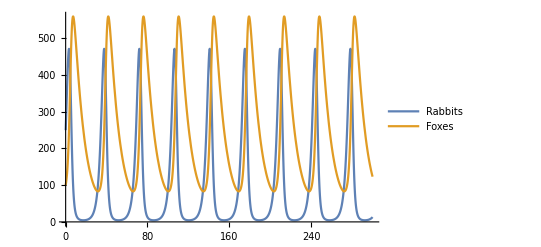

```mathematica
sol=NDSolve[{x'[t]==0.5*x[t]-0.002*x[t]*y[t], y'[t]==-0.1*y[t]+0.001*x[t]*y[t], x[0]==250,y[0]==100},{x,y},{t,0,300}];
Plot[{Evaluate[{x[t]}/.sol],Evaluate[{y[t]}/.sol]},{t,0,300},PlotLegends->{"Rabbits","Foxes"}]
```

# Practise 2

## 2.4 The heat equation on R

### a) Write a program in Mathematica that

#### a1)

```mathematica
fi[x_]:=Exp[-x^2]
```

```mathematica
nu=1
```

1

```mathematica
uapprox[x_,t_]:=(1/(√(4Pi nu t)))Integrate[Exp[(-(x-y)^2)/(4 nu t)]fi[y],{y, -∞, ∞}]
```

```mathematica
uapprox[x,t]
```

ConditionalExpression[(ⅇ^(-x^2/(1+4 t)))/(√(4+1/t) √t),Re[1/t]≥-4]

#### a2) Verify that the solution satisfies the heat equation (2.20)

```mathematica
D[uapprox,t]-nu D[uapprox,{x,2}]
```

0

```mathematica
uapprox[x,0]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Integrate::idiv: Integral of Indeterminate does not converge on {-∞,∞}.

ComplexInfinity

#### a3) Plot the solution for -6 <= x <= 6 and 0 <= t <= 4

```mathematica
Plot3D[uapprox[x,t],{x,-6,6},{t,0,4},PlotRange -> All, DisplayFunction-> Identity,AxesLabel -> {"x","t", "u"}]
```

General::munfl: Exp[-31459.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1007.97] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics3D-

#### a4) Plot the contour plot of the solution, for example, for -6 <= x <= 6 and 0 <= t <= 4

General::munfl: Exp[-31491.] is too small to represent as a normalized machine number; precision may be lost.

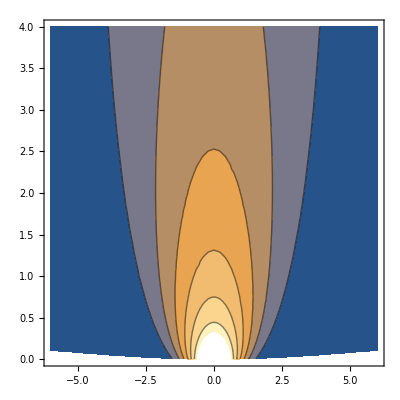

```mathematica
ContourPlot[uapprox[x,t],{x,-6,6},{t,0,4}]
```

## 2.5 The wave equation on R

### a) Write a program in Mathematica that

#### a1) Define the solution (2.24) for the particular problems with c = 1 and fi21[x] = Exp[-x^2], psi21[x] = 0 and fi22[x] = 0, psi21[x] = Exp[-x^2]

```mathematica
Clear["Global`*"]
```

```mathematica
fi21[x_]:=Exp[-x^2]
psi21[x_]:=0
c=1
```

1

```mathematica
uapprox21[x_,t_]:=(1/2)*(fi21[x+ c*t] + fi21[x- c*t] ) + (1/(2 c))*Integrate[psi21[s],{s,x- c*t, x+ c*t}]
```

```mathematica
uapprox21[x,t]
```

1/2 (ⅇ^(-(-t+x)^2)+ⅇ^(-(t+x)^2))

```mathematica
fi22[x_]:=0
psi22[x_]:= Exp[-x^2]
```

```mathematica
uapprox22[x_,t_]:=(1/2)*(fi22[x+ c*t] + fi22[x- c*t] ) + (1/(2 c))Integrate[psi22[s],{s,x- c*t, x+ c*t}]
```

```mathematica
uapprox22[x,t]
```

1/4 √π (Erf[t-x]+Erf[t+x])

#### a2) Verify that the solution satisfy the wave equation (2.23)

```mathematica
D[uapprox21[x,t],{t,2}]-c^2*D[uapprox21[x,t],{x,2}]
```

1/2 (2 ⅇ^(-(-t+x)^2)+2 ⅇ^(-(t+x)^2)-4 ⅇ^(-(-t+x)^2) (-t+x)^2-4 ⅇ^(-(t+x)^2) (t+x)^2)+1/2 (-2 ⅇ^(-(-t+x)^2)-2 ⅇ^(-(t+x)^2)+4 ⅇ^(-(-t+x)^2) (-t+x)^2+4 ⅇ^(-(t+x)^2) (t+x)^2)

```mathematica
FullSimplify[D[uapprox21[x,t],{t,2}]-c^2*D[uapprox21[x,t],{x,2}]]
```

0

```mathematica
D[uapprox22[x,t],{t,2}]-c^2*D[uapprox22[x,t],{x,2}]
```

0

```mathematica
FullSimplify[uapprox21[x,0]-Exp[-x^2]]
```

0

```mathematica
ut21[x_,t_]=D[uapprox21[x,t],t];
```

```mathematica
ut21[x,0]
```

0

```mathematica
FullSimplify[uapprox22[x,0]]
```

0

```mathematica
ut22[x_,t_]=D[uapprox22[x,t],t];
```

```mathematica
ut22[x,0]-Exp[-x^2]
```

0

#### a3) Plot the solutions.............

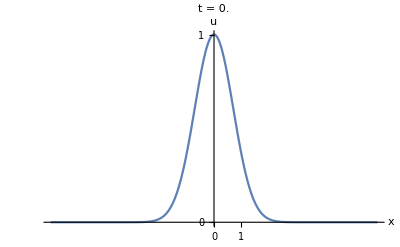
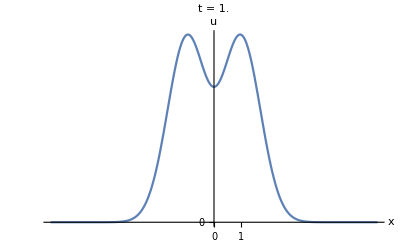
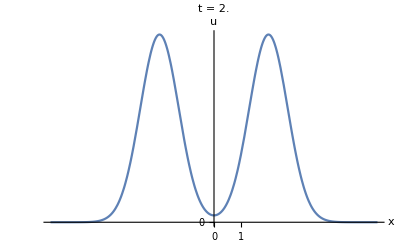
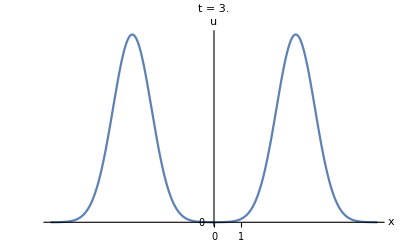

```mathematica
graphs=Table[Plot[uapprox21[x,t],{x,-6,6},PlotRange->All,Ticks->{{0,1},{0,1}},DisplayFunction->Identity,AxesLabel->{"x","u"},PlotLabel->"t = "<>ToString[N[t]]],{t,0,3,1}]
```

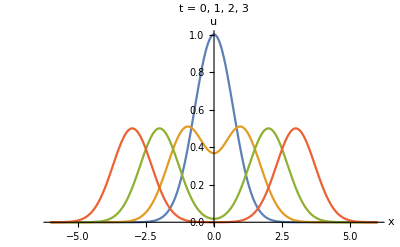

```mathematica
Plot[{uapprox21[x,0],uapprox21[x,1],uapprox21[x,2],uapprox21[x,3]},{x,-6,6},PlotRange -> All, DisplayFunction-> Identity,AxesLabel -> {"x", "u"}, PlotLabel -> "t = 0, 1, 2, 3"]
```

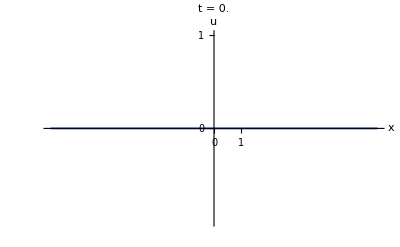
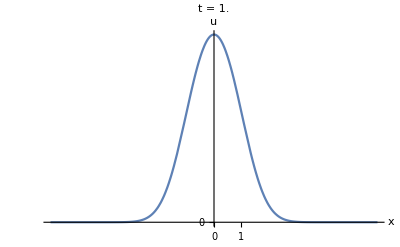
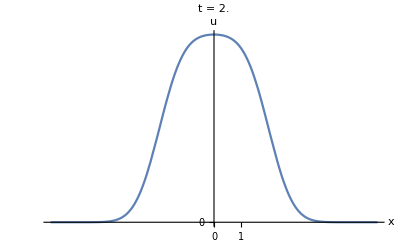
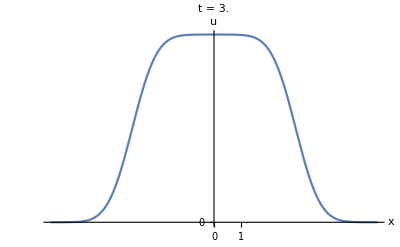

```mathematica
graphs=Table[Plot[uapprox22[x,t],{x,-6,6},PlotRange->All,Ticks->{{0,1},{0,1}},DisplayFunction->Identity,AxesLabel->{"x","u"},PlotLabel->"t = "<>ToString[N[t]]],{t,0,3,1}]
```

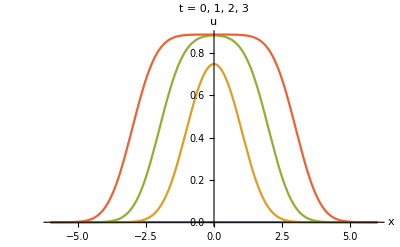

```mathematica
Plot[{uapprox22[x,0],uapprox22[x,1],uapprox22[x,2],uapprox22[x,3]},{x,-6,6},PlotRange -> All, DisplayFunction-> Identity,AxesLabel -> {"x", "u"}, PlotLabel -> "t = 0, 1, 2, 3"]
```

#### a4) Plot the 3D graphic........

```mathematica
Plot3D[uapprox21[x,t],{x,-6,6},{t,0,6},PlotRange -> All, DisplayFunction-> Identity,AxesLabel -> {"x","t", "u"}]
```

-Graphics3D-

```mathematica
Plot3D[uapprox22[x,t],{x,-6,6},{t,0,6},PlotRange -> All, DisplayFunction-> Identity,AxesLabel -> {"x","t", "u"}]
```

-Graphics3D-

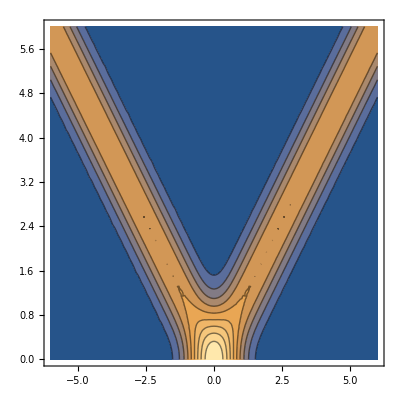

```mathematica
ContourPlot[uapprox21[x,t],{x,-6,6},{t,0,6}]
```

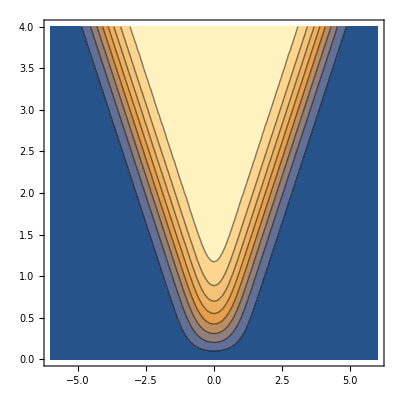

```mathematica
ContourPlot[uapprox22[x,t],{x,-6,6},{t,0,4}]
```

#### a6) What is the function that is part of the solution problem (2.26)? How is it defined?

## 2.6 The Laplace’s equation on R^2

### a) Write a program in Mathematica that

#### a1) Define the solution (2.28) for the particular problem with psi[x] = 1/(1 + x^2) and psi[x] = 0

```mathematica
psi3[x_]:= 0
fi3[x_]:=1/(1 + x^2)
```

```mathematica
uapprox3[x_,y_]:=1/2(fi3[x+ I y] + fi3[x- I y] ) - I/2 Integrate[psi3[s],{s,x- I y, x+ I y}]
```

```mathematica
uapprox3[x,y]
```

1/2 (1/(1+(x-ⅈ y)^2)+1/(1+(x+ⅈ y)^2))

#### a2) Verify that the solution satisfies the heat equation

```mathematica
D[uapprox3,{x,2}]+D[uapprox3,{y,2}]
```

0

```mathematica
uapprox3[x,0]==fi3[x]
```

True

```mathematica
uapprox3y[x_,y_]=D[uapprox3[x,y],y]//Simplify
```

(2 y (-3 x^4+(-1+y^2)^2-2 x^2 (1+y^2)))/((x^4+(-1+y^2)^2+2 x^2 (1+y^2))^2)

```mathematica
uapprox3y[x,0]
```

0

```mathematica
uapprox3y[x,0]==psi3[x]
```

True

#### a3) Plot the 3D graphic of the solution for -2 < = x, y <= 2

```mathematica
Plot3D[uapprox3[x,y],{x,-2,2},{y,-2,2},PlotRange-> All, DisplayFunction-> Identity,AxesLabel -> {"x","t", "u"}]
```

-Graphics3D-

#### a4) Plot the contour plot of the solution, for example, for ....

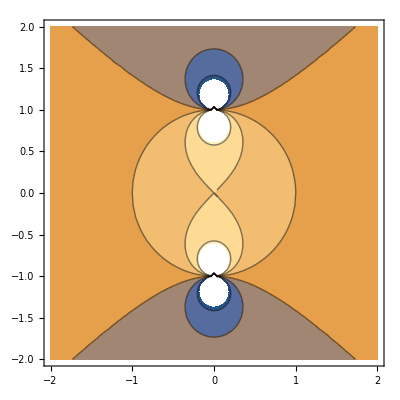

```mathematica
ContourPlot[uapprox3[x,y],{x,-2,2},{y,-2,2}]
```